## I. Spectrum Fit Template for Rovibrational Spectroscopy

Note: CGS units are used in this notebook.

#### Useful constants

cgs (centimeter-gram-seconds) units are most useful since we will use wavenumbuers for the peak positions.

```mathematica
hplanck = 6.62607004*10^(-34) (*J s*)
clight = 29979245800 (* cm / s *)
amu2kg= 1.660538782*10^(−27) (* kg / amu *)
Rideal = 8.3144598 (*J/(mol K) *)
```

6.62607×10^-34

29979245800

1.66054×10^-27

8.31446

#### Isotopic Masses

Below are the isotopic masses that are most relevant for Experiment 37. If you use this notebook for other elements, don’t forget to look them up here.

```mathematica
Hmass = amu2kg* 1.00782503223 (* kg *)
Dmass =amu2kg* 2.01410177812 (* kg *)
Cl35mass = amu2kg*34.968852682 (* kg *)
Cl37mass = amu2kg*36.965902602 (* kg *)
```

1.67353×10^-27

3.34449×10^-27

5.80671×10^-26

6.13833×10^-26

### A. Background and outcomes

In the experimental section of this lab you measured the peak positions of the P & R branches of the vibrational spectrum for HCl and DCl. You also identified the m values for each transition, where m is the quantum number that determines which peak in the P & R branches one is referring to.  The equation relating the peak position (in cm^-1) and the m quantum number is 
	ν(m)  = ν_0 + (2 B_e - 2 α_e) m - α m^2 
This equation itself is a simplification of the two equations needed to describe the P & R branches in terms of the quantum number J”, which actually labels the vibrational states (remember m labels the difference between two states!). See the pre-lab slides for a graphical connection between J” and m for an example spectra.

In this portion of the data analysis, you will read in your experimental data as instructed below and perform a nonlinear fit of the data. By the end of this section you will have computed a nonlinear fit of your experimental data in order to determine the rotational constants of HCl, which can then be used to determine the bond length between hydrogen and chlorine. Note: this process can be applied to other diatomic molecules, so save this notebook for future use in the second half of this experiment.

### B. Helper functions to simply the fitting procedure

In order to facilitate the fitting procedure, several functions have been created below. Each function takes a set of inputs and gives you an output. The details of each function are summarized in the comments contained between the “(***  ***)” characters. Execute the code blocks below to make these functions available to you.

The quadfit helper function is designed to save you time and repetition. You provide a list of input data with columns labeled as m, m^2, and ν (where ν are the peak positions in cm^-1), and the function gives you back a NonlinearModelFit object as output, assuming the model function:
	f(x,y) = c0 + c1 x + c2 x^2
which is the same we used previously in your homework. Execute code block I.B.1 below to store the function inside Mathematica’s kernel.

#### Code Block I.B.1 : quadfit helper function

```mathematica
quadfit[data_]:=Block[{x,nlm,c0,c1,c2,c3,model},
(*** Assumes data is organized in columns: m, m^2, ν 
Input : list of experimental results for quantum numbers and peak positions;
 Output : A NonlinearModelFit object 
***)
model = c0 + c1 x + c2 x^2+c3*x^3;
nlm = NonlinearModelFit[data,model,{c0,c1,c2,c3},{x}]
]
```

### C. Import experimental data and make initial nonlinear fit

In this section you will import your data and then make a ListPlot to check it.

#### Code Block I.C.1 : Import experimental data

Update the filepath to point to your experimental data. You should use a CSV file, like you have done previously for the OLS notebook in PChem I Lab. The order of the columns should be m, ν. Make sure than npeaks is equal to the number of peak positions that you identified.

```mathematica
fulldata = Import["/Users/batesje/Downloads/Copy of Rovib-CO raw data.xlsx - Fundamental.csv","CSV"]
(*"/Users/batesje/Dropbox/asu/teaching/F17/CHE3303/hcl_data.dat"]*)
npeaks = Length[fulldata]
```

{{-26,2032.25},{-25,2036.93},{-24,2041.59},{-23,2046.15},{-22,2050.76},{-21,2055.3},{-20,2059.82},{-19,2064.3},{-18,2068.75},{-17,2073.2},{-16,2077.52},{-15,2081.9},{-14,2086.23},{-13,2090.51},{-12,2094.76},{-11,2098.99},{-10,2103.17},{-9,2107.33},{-8,2111.45},{-7,2115.52},{-6,2119.59},{-5,2123.6},{-4,2127.59},{-3,2131.53},{-2,2135.45},{-1,2139.33},{1,2146.99},{2,2150.75},{3,2154.5},{4,2158.2},{5,2161.87},{6,2165.5},{7,2169.1},{8,2172.65},{9,2176.18},{10,2179.67},{11,2183.12},{12,2186.53},{13,2189.91},{14,2193.26},{15,2196.56},{16,2199.83},{17,2203.06},{18,2206.25},{19,2209.4},{20,2212.52},{21,2215.61},{22,2218.64},{23,2221.64},{24,2224.62},{25,2227.54},{26,2230.4},{27,2233.27},{28,2236.08},{29,2238.84},{30,2241.62},{31,2244.26}}

57

Double check that your data was read in properly and that it looks non-linear (roughly quadratic, like an inverted parabola).

#### Code Block I.C.2 : ListPlot experimental data

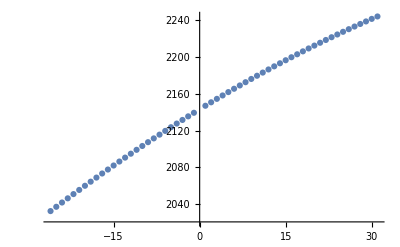

```mathematica
ListPlot[fulldata[[All,{1,2}]]]
```

Now use the quadfit helper function to make an initial fit of the data. We will save the initial fit as nlm0.

#### Code Block I.C.3 : quadfit experimental data

```mathematica
nlm0 = quadfit[fulldata]
```

FittedModel[2143.17+3.8273 x-«21» «1»-0.0000242429 x^3]

#### Code Block I.C.4: Extract the quality of fit, fit parameters, and uncertainties in the fit parameters from your data

The nlm0 object created in Code Block I.C.3 contains a lot of information. You can extract the quality of fit (aka : R^2), the fit parameters, and the uncertainties in the fit parameters from the nlm0 object produced in Code Block I.C.3 using the following commands:

```mathematica
rsqnlm = nlm0["RSquared"] (*This is the R^2 value*)
nlmfit1= {c0,c1,c2,c3}/.nlm0["BestFitParameters"] (*this is a list of the 3 fit parameters*)
nlmfit1err = nlm0["ParameterErrors"] (*this is a list of the uncertainties in the fit parameters*)
```

1.

{2143.17,3.8273,-0.0175064,-0.0000242429}

{0.00232615,0.000218241,6.76278×10^-6,4.05918×10^-7}

```mathematica
(nlmfit1[[2]]-2nlmfit1[[3]])/2
```

1.93116

To access individual values, use “list referencing.” For example, if you want to extract the 2nd fit constant in the list above nlmfit1 --> nlmfit1[[ 2 ]]. PLEASE AVOID TRYING TO COPY AND PASTE THESE VALUES. If you use list referencing, you will create an internally linked tool, much like an Excel sheet where you reference specific rows and columns.

```mathematica
nlmfit1[[2]]
```

3.8273

### Exercise I. Process results and compute rotational constants & bond length

#### 1. Compute the rotational constants from the fit parameters

Using the formulas given in the Handout & pre-lab lecture, compute the rotational constants (α_e & β_e), the moment of inertia (I), and the bond length of the molecule. 
Remember to use list references to extract the individual fit parameter values for use below.
Hint: Start with the calculation of your reduced mass, that way you know where you need to make changes when analyzing subsequent molecules.

#### 2. Compare to a reference value

Look up a reference value for these constants on the NIST webbook, and write a complete sentence comparing the equilibrium bond length, and the first and second rotational constants between NIST and your results.